```mathematica
CVertex[name_,position_,boundary_]:=CVertex[Hold[name,position,boundary]]
```

```mathematica
VertexData[c_CVertex]:=Level[Level[c,1][[1]],1]
```

```mathematica
example1=CVertex[a,{1,1},b]
```

CVertex[Hold[a,{1,1},b]]

```mathematica
VertexData[example1]
```

{a,{1,1},b}

```mathematica
ZZComplex[vertices_List]:=Module[{newvert=}]
```

```mathematica
ZZComplex[{example1,example1}]
```

ZZComplex[{CVertex[Hold[a,{1,1},b]],CVertex[Hold[a,{1,1},b]]}]

```mathematica
ZZComplex[vertices_List,edges_List]:=ZZComplex[Hold[vertices,edges]]

ZZComplex[example1,example1]
```

ZZComplex[CVertex[Hold[a,{1,1},b]],CVertex[Hold[a,{1,1},b]]]

```mathematica
CVertexList[A_ZZComplex]:=Level[Level[A,1][[1]],1][[1]]
```

```mathematica
CEdgeList[A_ZZComplex]:=Level[Level[A,1][[1]],1][[2]]
```

```mathematica
BasisSwap[A_ZZComplex,a_,b_]:=Module[{newgens=CVertexList[A]},newgens[[b,1]]=PolynomialMod[newgens[[b,1]]+newgens[[a,1]],2];newgens]
```

```mathematica
c1=StaircaseComplex[{1,1}]
```

ZZComplex[Hold[{{a[1],{0,1}},{a[2],{1,1}},{a[3],{1,0}}},{a[2]→a[1],a[2]→a[3]}]]

```mathematica
CChangeBasis[c1,2,1]
```

CChangeBasis[ZZComplex[Hold[{{a[1],{0,1}},{a[2],{1,1}},{a[3],{1,0}}},{a[2]→a[1],a[2]→a[3]}]],2,1]

```mathematica
FilteredCOB[A_ZZComplex,a_,b_]:=Module[{vlist=CVertexList[A],elist=CEdgeList[A]},
If[
vlist[[b,2,1]]≥vlist[[a,2,1]]&&vlist[[b,2,2]]≥vlist[[a,2,2]]&&a≠b,
ZZComplex[BasisSwap[A,a,b],elist],A
]
]
```

```mathematica
FilteredCOB[c1,3,2]
```

ZZComplex[Hold[{{a[1],{0,1}},{a[2]+a[3],{1,1}},{a[3],{1,0}}},{a[2]→a[1],a[2]→a[3]}]]

```mathematica
PolynomialMod[2a[2],2]
```

0

```mathematica
StaircaseComplex[gaps_List,var_]:=
With[
{
coordinates=With[
{table=Table[
{
Sum[gaps[[2j-1]],{j,1,i}],
Sum[gaps[[2k]],{k,i,Length[gaps]/2}]
},
{i,1,Length[gaps]/2}]
},
Append[
Riffle[
table-Table[{gaps[[2i-1]],0},{i,1,Length[gaps]/2}],
table],
table[[-1]]-{0,gaps[[-1]]}
]
]
},
With[{vertices=
Table[
{var[i],coordinates[[i]]},
{i,1,Length[coordinates]}
]},

ZZComplex[vertices,
Riffle[
Table[vertices[[2i]][[1]]->vertices[[2i-1]][[1]],{i,1,(Length[vertices]-1)/2}],Table[vertices[[2i]][[1]]->vertices[[2i+1]][[1]],{i,1,(Length[vertices]-1)/2}]]

]]]

Table[Sum[i,{i,1,10}],{j,1,10}]
```

{55,55,55,55,55,55,55,55,55,55}

```mathematica
StaircaseComplex[gaps_List]:=StaircaseComplex[gaps,a]

complexdude = StaircaseComplex[{1,2,3,3,2,1}]
```

ZZComplex[Hold[{{a[1],{0,6}},{a[2],{1,6}},{a[3],{1,4}},{a[4],{4,4}},{a[5],{4,1}},{a[6],{6,1}},{a[7],{6,0}}},{a[2]→a[1],a[2]→a[3],a[4]→a[3],a[4]→a[5],a[6]→a[5],a[6]→a[7]}]]

```mathematica
CTensor[A_ZZComplex,B_ZZComplex]:=Module[
{
Avlist=CVertexList[A],
Bvlist=CVertexList[B],
Aelist=CEdgeList[A],
Belist=CEdgeList[B]
},
ZZComplex[

Flatten[
Table[
{Avlist[[j]][[1]]⊗Bvlist[[i]][[1]],Avlist[[j]][[2]]+Bvlist[[i]][[2]]},
{j,1,Length[Avlist]},
{i,1,Length[Bvlist]}
],1
],

Flatten[Join
[
Table[Aelist/.Table[Avlist[[i,1]]->Avlist[[i,1]]⊗Bvlist[[j,1]],{i,1,Length[Avlist]}],{j,1,Length[Bvlist]}],
Table[Belist/.Table[Bvlist[[i,1]]->Avlist[[j,1]]⊗Bvlist[[i,1]],{i,1,Length[Bvlist]}],{j,1,Length[Avlist]}]

]
]
]
]
```

```mathematica
PosAug[list_,arg_,val_]:=Block[
{l},
l=list;
If[
MemberQ[Part[l,1;;arg-1],l[[arg]]],
l[[arg]]+=val;l,
l]
]
```

```mathematica
PosSimp[list_,arg_]:=Fold[PosAug[#1,arg,#2]&,list,{{.2,.2},{-.4,-.4},{.4,0},{-.4,.4}}]
```

```mathematica
FullSimp[list_]:=Fold[PosSimp[#1,#2]&,list,Range[Length[list]]]
```

```mathematica
AdjustVertexPosition[A_ZZComplex]:=Module[{vlist=CVertexList[A],
elist=CEdgeList[A],poslist=Table[CVertexList[A][[i]][[2]],{i,1,Length[CVertexList[A]]}]
},
With[{newplist=FullSimp[poslist]},
ZZComplex[
Table[{vlist[[i,1]],newplist[[i]]},{i,1,Length[vlist]}],
elist
]
]
]
```

```mathematica
test4:={{a,{4,4}},{b,{4,4}},{c,{4,4}},{d,{4,4}},{e,{4,4}}}
```

```mathematica
AdjustVertexPosition[ZZComplex[test4,{a->b,b->c}]]
```

ZZComplex[Hold[{{a,{4,4}},{b,{4.2,4.2}},{c,{3.8,3.8}},{d,{4.2,3.8}},{e,{3.8,4.2}}},{a→b,b→c}]]

```mathematica
CSimplePlot[A_ZZComplex]:=
Module[

{
coords=CVertexList[A]
},

GraphPlot[
Level[Level[A,1][[1]],1][[2]],
VertexCoordinateRules->Table[coords[[i]][[1]]->coords[[i]][[2]],{i,1,Length[coords]}],
MultiedgeStyle->1,
VertexLabeling->False
]

]
```

```mathematica
CPlot[A_ZZComplex]:=
CSimplePlot[AdjustVertexPosition[A]]
```

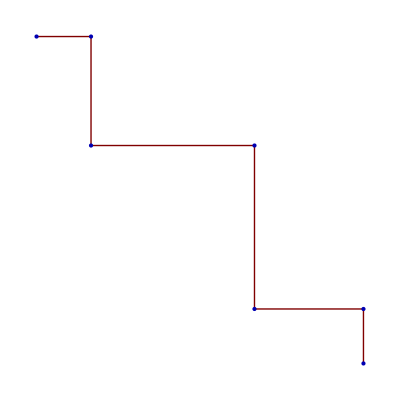

```mathematica
CPlot[StaircaseComplex[{1,2,3,3,2,1}]]
```

```mathematica
A1:=StaircaseComplex[{1,1,1,1},a]
B1:=StaircaseComplex[{2,2},b]
```

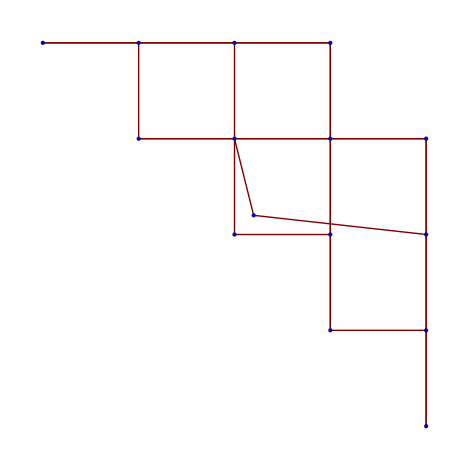

```mathematica
CPlot[CTensor[A1,B1]]
```

```mathematica
TorusAlexP[p_,q_]:=PolynomialQuotient[((t-1)(t^(p q)-1)),((t^p-1)(t^q-1)),t]
```

```mathematica
T[p_,q_]:=T[Hold[TorusAlexP[p,q]]]
```

```mathematica
Δ[knot_T]:=ReleaseHold@@knot
```

```mathematica
Δ[T[2,3]]
```

1-t+t^2

```mathematica
CInvariantList[K_]:=Module[{reductionlist=NestWhileList[PolynomialMod[#,t^Exponent[#,t]]&,K,Exponent[#,t]>0&]},Table[Exponent[reductionlist[[i]],t]-Exponent[reductionlist[[i+1]],t],{i,1,Length[reductionlist]-1}]]
```

```mathematica
CInvariant[K_T]:=StaircaseComplex[CInvariantList[Δ[K]]]
```

```mathematica
Manipulate[CPlot[Nest[CTensor[#,CInvariant[T[2,3]]]&,CInvariant[T[2,3]],n]],{n,0,6,1}]
```

```mathematica
T[2,3]
```

T[Hold[TorusAlexP[2,3]]]

```mathematica
T[Hold[TorusAlexP[2,3]]]
```

T[Hold[TorusAlexP[2,3]]]

```mathematica
KnotCable[polynomial_,p_,q_]:=Expand[(polynomial/.t->t^p)*TorusAlexP[p,q]]
```

```mathematica
threefourcable := KnotCable[Δ[T[2,3]],3,4]
```

```mathematica
fourfivecable := KnotCable[Δ[T[2,3]],4,5]
```

```mathematica
cat:=CTensor[StaircaseComplex[CInvariantList[threefourcable]],StaircaseComplex[CInvariantList[fourfivecable]]]
```

```mathematica
ColumnVertices[complex_ZZComplex]:=Table[Select[CVertexList[complex],MatchQ[#,List[_,List[i,_]]]&],{i,LowestRowIndex[complex],HighestRowIndex[complex]}]
LowestRowIndex[complex_ZZComplex]:=Min[Table[Level[CVertexList[complex],2][[3*i-1]][[1]],{i,1,Length[CVertexList[complex]]}]]
HighestRowIndex[complex_ZZComplex] := Max[Table[Level[CVertexList[complex],2][[3*i-1]][[1]],{i,1,Length[CVertexList[complex]]}]]
```

```mathematica
ColumnEdges[edges_List,points_List]:= Select[Select[edges,MemberQ[points,Level[#,1][[1]]]&],MemberQ[points,Level[#,1][[2]]]&]
```

```mathematica
CComplexColumn[number_,complex_ZZComplex]:= Module[
{ vertices = ColumnVertices[complex][[number]],
points = ColumnVertices[complex][[number]] ,
edges = ColumnEdges[CEdgeList[complex],Select[Level[ColumnVertices[complex][[number]],2], Head[#]==  CircleTimes&]]
},
ZZComplex[points,edges]
]
```

```mathematica
CComplexHomology[complex_ZZComplex]:={CCKernel[complex],CCImage[complex]}

CCKernel[complex_ZZComplex]:= Select[CVertexListNoCoords[complex],!MemberQ[CCArrowsOutgoing[complex],#] &]
CCArrowsOutgoing[complex_ZZComplex]:=Union[Table[Level[CEdgeList[complex],2][[3*i+1]],{i,0,Length[CEdgeList[complex]]-1}]]
CCImage[complex_ZZComplex]:=Union[Table[Level[CEdgeList[complex],2][[3*i+2]],{i,0,Length[CEdgeList[complex]]-1}]]
```

```mathematica
HomologyNonZeroTest[complex_ZZComplex]:= Length[CComplexHomology[complex][[1]]]>Length[CComplexHomology[complex][[2]]]
```

```mathematica
CVertexListNoCoords[complex_ZZComplex]:=Table[Level[CVertexList[complex],2][[3*i-2]],{i,1,Length[CVertexList[complex]]}]
```

```mathematica
ducat=CComplexColumn[3,cat]
```

ZZComplex[Hold[{{a[1]⊗a[4],{2,12}},{a[1]⊗a[5],{2,10}},{a[2]⊗a[2],{2,16}},{a[2]⊗a[3],{2,12}},{a[3]⊗a[2],{2,13}},{a[3]⊗a[3],{2,9}},{a[4]⊗a[1],{2,13}},{a[5]⊗a[1],{2,12}}},{a[4]⊗a[1]→a[5]⊗a[1],a[2]⊗a[2]→a[3]⊗a[2],a[2]⊗a[3]→a[3]⊗a[3],a[1]⊗a[4]→a[1]⊗a[5],a[2]⊗a[2]→a[2]⊗a[3],a[3]⊗a[2]→a[3]⊗a[3]}]]

```mathematica
LowestLevel[complex_ZZComplex]:= Min[Table[Level[CVertexList[complex],2][[3*i-1]][[2]],{i,1,Length[CVertexList[complex]]}]]
```

```mathematica
HighestLevel[complex_ZZComplex]:=Max[Table[Level[CVertexList[complex],2][[3*i-1]][[2]],{i,1,Length[CVertexList[complex]]}]]
```

```mathematica
dog:=CPlot[CTensor[StaircaseComplex[CInvariantList[threefourcable]],StaircaseComplex[CInvariantList[fourfivecable]]]]
```

```mathematica
CPlot[CTensor[StairStaircaseComplex[{-1,-2,-2,-1}]]
```

```mathematica
CInvariantList[fourfivecable]
```

{1,4,1,2,1,1,1,1,2,1,4,1}

```mathematica
Map[CInvariantList[threefourcable], RightArrow[x,-x]]
```

{1,3,1,1,1,1,3,1}[x]→{1,3,1,1,1,1,3,1}[-x]

```mathematica
f[x_]:= -x
```

```mathematica
Map[f,CInvariantList[threefourcable]]
```

{-1,-3,-1,-1,-1,-1,-3,-1}

```mathematica
dogdog:=CPlot[StaircaseComplex[CInvariantList[fivesixcable]]]
```

```mathematica
dogdogdog:=CPlot[StaircaseComplex[Map[f,CInvariantList[threefourcable]]]]
```

```mathematica
fivesixcable := KnotCable[Δ[T[2,3]],5,6]
```

```mathematica
charles:=CTensor[StaircaseComplex[CInvariantList[fourfivecable]],StaircaseComplex[Map[f,CInvariantList[threefourcable]]]]
```

```mathematica
CPlot[charles]
```

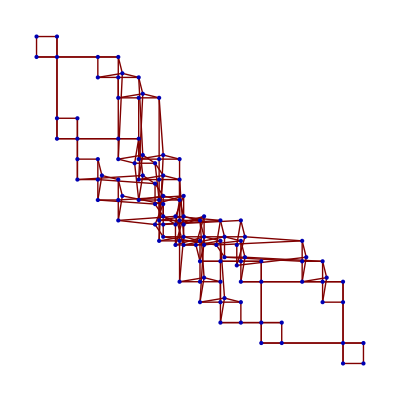

```mathematica
CVertexList[CComplexColumn[2,charles]]
```

{{a[2]⊗a[8],{-5,9}},{a[2]⊗a[9],{-5,10}},{a[3]⊗a[8],{-5,5}},{a[3]⊗a[9],{-5,6}}}

```mathematica
CEdgeList[CComplexColumn[2,charles]]
```

{a[2]⊗a[8]→a[3]⊗a[8],a[2]⊗a[9]→a[3]⊗a[9],a[2]⊗a[8]→a[2]⊗a[9],a[3]⊗a[8]→a[3]⊗a[9]}

```mathematica
CComplexHomology[CComplexColumn[2,charles]]
```

{{a[3]⊗a[9]},{a[2]⊗a[9],a[3]⊗a[8],a[3]⊗a[9]}}

```mathematica
HomologyNonZeroTest[CComplexColumn[6,charles]]
```

False